```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
R=0.07 10^8;(*in m*)
```

```mathematica
vesc=6 10^6;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
vtilde=247*10^3(*in m/sec*);
```

```mathematica
ρx=1 10^5  10^5;(*in GeV/m^3*)
```

```mathematica
mn=1.0;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
δ=10^-6;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1+1/(δ*(1-δ)^(N-1)))/((1-δ*βplus[mx])^(N-1)*(1-βplus[mx]+1/(δ*(1-δ)^(N-1))))-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/((1-βplus[mx])*(1-δ*βplus[mx])^(N-1))-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=δ*(1-δ)^(N-1)*(vesc^2-(u^2+vesc^2)*(1-βplus[mx])*(1-δ*βplus[mx])^(N-1))/((u^2+vesc^2)*(1-δ*βplus[mx])^(N-1)-vesc^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn;
```

```mathematica
tau[sigma_?NumericQ]:=(3*sigma)/(2*sigmaSat);
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N](tau[sigma])^2)(Gamma[N+2.0]-Gamma[N+2.0,tau[sigma]]);
```

```mathematica
(*pn[N_?NumericQ,sigma_?NumericQ]:=2/Factorial[N] NIntegrate[y Exp[-y tau[sigma]](y tau[sigma])^N,{y,0,1},AccuracyGoal->15,MaxRecursion->20]*)
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},AccuracyGoal->5,MaxRecursion->12,PrecisionGoal->3];
```

```mathematica
Nmax[mx_?NumericQ,sigma_?NumericQ]:=For[i=0,i≤ 10,i = i + 0.001,If[t* CNNboosted[10^i,mx,sigma]≤1,Return[Floor[10^i]];Break[]]];
```

```mathematica
Nmax2[mx_?NumericQ,sigma_?NumericQ]:=(temp=10^-2 CNNboosted[1,mx,sigma];For[j=1,j≤ 10,j=j+0.001,If[temp≥ CNNboosted[10^j,mx,sigma],Return[Floor[10^j]];Break[]]]);
```

```mathematica
Ctotalnew[mx_?NumericQ,sigma_?NumericQ]:=Sum[CNNboosted[int,mx,sigma],{int,1,Nmax[mx,sigma]}];
```

```mathematica
Ctotalnew2[mx_?NumericQ,sigma_?NumericQ]:=Sum[CNNboosted[int,mx,sigma],{int,1,Nmax2[mx,sigma]}];
```

```mathematica
Ctotalnew3[mx_?NumericQ,sigma_?NumericQ]:=(table=Table[CNNboosted[int,mx,sigma],{int,1,Nmax[mx,sigma]}];Total[table]);
```

```mathematica
(*threshold=0.1;
Ctotalnew2[mx_?NumericQ,sigma_?NumericQ]:=
(val=0;For[i1=1,i1≤Nmax[mx,sigma],i1++, If[Abs[CNNboosted[i1+1,mx,sigma]-CNNboosted[i1,mx,sigma]]<threshold ,Break[],val=CNNboosted[i1,mx,sigma]+val]];Return[val]);*)
```

```mathematica
(*myticks={{Automatic,None},{{{-6,"10^-6"},{-2,"10^-2"},{2,"10^2"},{6,"10^6"}},None}};*)
```

```mathematica
(*p=ListLogPlot[{Table[{x,Ctotalnew[10^x,10^-45]},{x,-6,5,0.5}],Table[{x,CNNboosted[1,10^x,10^-45]},{x,-6,5,0.5}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-6,Automatic},FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["Number of Captured DM",FontSize->20,Bold]},PlotLegends->{"Total Number of DM captured","Number of DM captured after first scattering"},ImageSize->500,FrameLabel-> "Light mediator case"]*)
```

```mathematica
(*p2=ListLogPlot[{Table[{x,10^x Ctotalnew[10^x,10^-45]},{x,-6,3}],Table[{x,10^x Ctotalnew[10^x,10^-50]},{x,-6,3}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},PlotRange->Automatic,Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin-> {-6,Automatic},FrameLabel->{Style["Mass of DM [GeV]",FontSize->20,Bold],Style["M_DM x C_Tot",FontSize->20,Bold]},PlotLegends->{"σ = 10^-45 m^2","σ = 10^-50 m^2"},ImageSize->500]*)
```

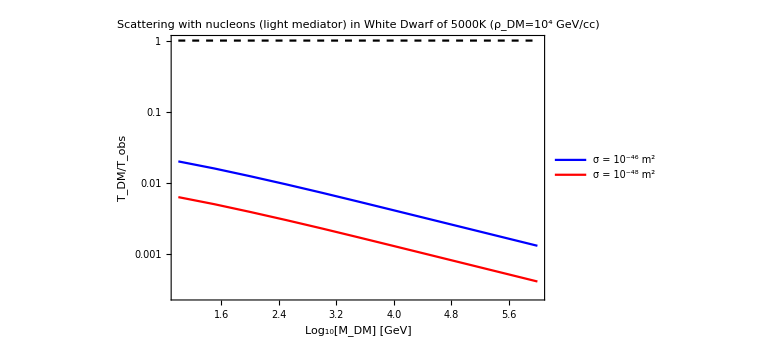

```mathematica
plotElecWD3=ListLogPlot[{Table[{x,(1/10^33 10^x Ctotalnew[10^x,10^-46])^0.25},{x,1,6,0.5}],Table[{x,(1/10^33 10^x Ctotalnew[10^x,10^-48])^0.25},{x,1,6,0.5}],Table[{x,(1/10^33 10^x Ctotalnew[10^x,10^-50])^0.25},{x,1,6,0.5}],Table[{x,1},{x,1,6,0.5}]},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}},PlotRange->Full,Frame->True,Joined-> True,AxesOrigin ->{Automatic,Automatic},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["T_DM/T_obs",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-46 m^2","σ = 10^-48 m^2"},Top],PlotLabel->"Scattering with nucleons (light mediator) in White Dwarf of 5000K (ρ_DM=10^4 GeV/cc)"]
```

```mathematica
Export["plotWD5.pdf",plotElecWD3];
```